```mathematica
EOM=D[𝒳,{t,2}]==(({{1, 0, 0}, {0, 1, 0}, {0, 0, -α}})(1-1/A)).Subscript[𝒱, 1]+(κ({{1, 0, 0}, {0, 1, 0}, {0, 0, -α}})(1-1/B ℒ)).Subscript[𝒱, 2]-({{0}, {γ}, {0}})//Flatten;
{Subscript[x, 1][t]=Subscript[y, 1][t]=Subscript[y, 2][t]=0,Subscript[x, 2][t]=2 Subscript[w, p],
Subscript[θ, p][t]->0} :{Subscript[x, p][t]->Subscript[w, p],Subscript[y, p][t]->1/2 (-2-γ-2 Subscript[h, p])}
```

```mathematica
perturbations:
```

```mathematica
EquilibiumPoinit={Subscript[Subscript[θ, p], 0]->0, Subscript[Subscript[x, p], 0]->Subscript[w, p],Subscript[Subscript[y, p], 0]->-(1/2 γ+Subscript[h, p]+1)}
GivenEquibPoints={Subscript[x, 1][t]->0,Subscript[y, 1][t]->0,Subscript[y, 2][t]->0,Subscript[x, 2][t]->2 Subscript[w, p]}
perturb={
Subscript[θ, p][t]->Subscript[Subscript[θ, p], 0]+δθ[t],
Subscript[x, p][t]->Subscript[Subscript[x, p], 0]+δx[t],
Subscript[y, p][t]->Subscript[Subscript[y, p], 0]+δy[t]
}
perturbD2={
D[Subscript[θ, p][t],{t,2}]->D[δθ[t],{t,2}],
D[Subscript[x, p][t],{t,2}]->D[δx[t],{t,2}],
D[Subscript[y, p][t],{t,2}]->D[δy[t],{t,2}]
}
```

{θ_p_0→0,x_p_0→w_p,y_p_0→-1-γ/2-h_p}

{x_1[t]→0,y_1[t]→0,y_2[t]→0,x_2[t]→2 w_p}

{θ_p[t]→θ_p_0+δθ[t],x_p[t]→x_p_0+δx[t],y_p[t]→y_p_0+δy[t]}

{θ_p''[t]→δθ''[t],x_p''[t]→δx''[t],y_p''[t]→δy''[t]}

```mathematica
D[𝒳,{t,2}]/.perturbD2
```

{{δx''[t]},{δy''[t]},{δθ''[t]}}

```mathematica
Aw=A/.nameChange
```

√((Sin[θ_p[t]] h_p+Cos[θ_p[t]] w_p+x_1[t]-x_p[t])^2+(-Cos[θ_p[t]] h_p+Sin[θ_p[t]] w_p+y_1[t]-y_p[t])^2)

```mathematica
Bw=B/.nameChange
```

√((Sin[θ_p[t]] h_p-Cos[θ_p[t]] w_p+x_2[t]-x_p[t])^2+(-Cos[θ_p[t]] h_p-Sin[θ_p[t]] w_p+y_2[t]-y_p[t])^2)

```mathematica
smallAngleRule={Cos[δθ[t]]->1,Sin[δθ[t]]->δθ[t]}
```

{Cos[δθ[t]]→1,Sin[δθ[t]]→δθ[t]}

```mathematica
(v1=Subscript[𝒱, 1]/.nameChange/.perturb/.EquilibiumPoinit/.smallAngleRule)//TraditionalForm
(v2=Subscript[𝒱, 2]/.nameChange/.perturb/.EquilibiumPoinit/.smallAngleRule)//TraditionalForm
```

(-δx(t)+h_p δθ(t)+x_1(t)
γ/2-δy(t)+w_p δθ(t)+y_1(t)+1
w_p (γ/2+h_p-δy(t)-δθ(t) (-w_p-δx(t)+x_1(t))+y_1(t)+1)+h_p (-w_p-δx(t)+x_1(t)+δθ(t) (γ/2+h_p-δy(t)+y_1(t)+1)))

(-2 w_p-δx(t)+h_p δθ(t)+x_2(t)
γ/2-δy(t)-w_p δθ(t)+y_2(t)+1
w_p (-γ/2-h_p+δy(t)+δθ(t) (-w_p-δx(t)+x_2(t))-y_2(t)-1)+h_p (-w_p-δx(t)+x_2(t)+δθ(t) (γ/2+h_p-δy(t)+y_2(t)+1)))

```mathematica
v1/.GivenEquibPoints//Simplify
v2/.GivenEquibPoints//Simplify
```

{{-δx[t]+h_p δθ[t]},{1+γ/2-δy[t]+w_p δθ[t]},{1/2 (2 w_p^2 δθ[t]+w_p (2+γ-2 δy[t]+2 δx[t] δθ[t])+h_p (-2 δx[t]+(2+γ+2 h_p-2 δy[t]) δθ[t]))}}

{{-δx[t]+h_p δθ[t]},{1/2 (2+γ-2 δy[t]-2 w_p δθ[t])},{w_p^2 δθ[t]-1/2 w_p (2+γ-2 δy[t]+2 δx[t] δθ[t])+1/2 h_p (-2 δx[t]+(2+γ+2 h_p-2 δy[t]) δθ[t])}}

```mathematica
(*D[Aw,Subscript[x, p][t]]
D[Aw,Subscript[y, p][t]]
D[Aw,Subscript[θ, p][t]]*)
temp={Subscript[x, p][t]->Subscript[Subscript[x, p], 0],Subscript[y, p][t]->Subscript[Subscript[y, p], 0],Subscript[θ, p][t]->Subscript[Subscript[θ, p], 0]};
"derivatives of 'A' in the 0 point:"
D[Aw^2,Subscript[x, p][t]]/.temp/.EquilibiumPoinit
D[Aw^2,Subscript[y, p][t]]/.temp/.EquilibiumPoinit
D[Aw^2,Subscript[θ, p][t]]/.temp/.EquilibiumPoinit
```

```mathematica
"derivatives of 'B' in the 0 point:"
D[Bw^2,Subscript[x, p][t]]/.temp/.EquilibiumPoinit
D[Bw^2,Subscript[y, p][t]]/.temp/.EquilibiumPoinit
D[Bw^2,Subscript[θ, p][t]]/.temp/.EquilibiumPoinit
```

derivatives of 'B' in the 0 point:

-2 (-2 w_p+x_2[t])

-2 (1+γ/2+y_2[t])

2 h_p (-2 w_p+x_2[t])-2 w_p (1+γ/2+y_2[t])

```mathematica
n=1;Ataylored=Series[Aw/.GivenEquibPoints,{Subscript[x, p][t],Subscript[Subscript[x, p], 0],n},{Subscript[y, p][t],Subscript[Subscript[y, p], 0],n},{Subscript[θ, p][t],Subscript[Subscript[θ, p], 0],n}]/.EquilibiumPoinit
```

((√((-1-γ/2-h_p)^2+2 (-1-γ/2-h_p) h_p+h_p^2)-(((-1-γ/2-h_p) w_p+h_p w_p) θ_p[t])/(√((-1-γ/2-h_p)^2+2 (-1-γ/2-h_p) h_p+h_p^2))+O[θ_p[t]]^2)+((-1-γ/2)/(√((-1-γ/2-h_p)^2+2 (-1-γ/2-h_p) h_p+h_p^2))+(-w_p/(√((-1-γ/2-h_p)^2+2 (-1-γ/2-h_p) h_p+h_p^2))+((-1-γ/2) ((-1-γ/2-h_p) w_p+h_p w_p))/(((-1-γ/2-h_p)^2+2 (-1-γ/2-h_p) h_p+h_p^2)^(3/2))) θ_p[t]+O[θ_p[t]]^2) (y_p[t]+1+γ/2+h_p)+O[y_p[t]+1+γ/2+h_p]^2)+((-(h_p θ_p[t])/(√((-1-γ/2-h_p)^2+2 (-1-γ/2-h_p) h_p+h_p^2))+O[θ_p[t]]^2)+(((-1-γ/2) h_p θ_p[t])/(((-1-γ/2-h_p)^2+2 (-1-γ/2-h_p) h_p+h_p^2)^(3/2))+O[θ_p[t]]^2) (y_p[t]+1+γ/2+h_p)+O[y_p[t]+1+γ/2+h_p]^2) (x_p[t]-w_p)+O[x_p[t]-w_p]^2

```mathematica
n=1;Series[Bw,{Subscript[x, p][t],Subscript[Subscript[x, p], 0],n},{Subscript[y, p][t],Subscript[Subscript[y, p], 0],n},{Subscript[θ, p][t],Subscript[Subscript[θ, p], 0],n}]/.EquilibiumPoinit
```

((√((-2 w_p+x_2[t])^2+(1+γ/2+y_2[t])^2)+((2 h_p (-2 w_p+x_2[t])+2 w_p (-1-γ/2-y_2[t])) θ_p[t])/(2 √((-2 w_p+x_2[t])^2+(1+γ/2+y_2[t])^2))+O[θ_p[t]]^2)+((-1-γ/2-y_2[t])/(√((-2 w_p+x_2[t])^2+(1+γ/2+y_2[t])^2))+(-((2 h_p (-2 w_p+x_2[t])+2 w_p (-1-γ/2-y_2[t])) (-1-γ/2-y_2[t]))/(2 ((-2 w_p+x_2[t])^2+(1+γ/2+y_2[t])^2)^(3/2))+w_p/(√((-2 w_p+x_2[t])^2+(1+γ/2+y_2[t])^2))) θ_p[t]+O[θ_p[t]]^2) (y_p[t]+1+γ/2+h_p)+O[y_p[t]+1+γ/2+h_p]^2)+(((2 w_p-x_2[t])/(√((-2 w_p+x_2[t])^2+(1+γ/2+y_2[t])^2))+(-((2 w_p-x_2[t]) (2 h_p (-2 w_p+x_2[t])+2 w_p (-1-γ/2-y_2[t])))/(2 ((-2 w_p+x_2[t])^2+(1+γ/2+y_2[t])^2)^(3/2))-h_p/(√((-2 w_p+x_2[t])^2+(1+γ/2+y_2[t])^2))) θ_p[t]+O[θ_p[t]]^2)+(((-2 w_p+x_2[t]) (-1-γ/2-y_2[t]))/(((-2 w_p+x_2[t])^2+(1+γ/2+y_2[t])^2)^(3/2))+(-(3 (-2 w_p+x_2[t]) (2 h_p (-2 w_p+x_2[t])+2 w_p (-1-γ/2-y_2[t])) (-1-γ/2-y_2[t]))/(2 ((-2 w_p+x_2[t])^2+(1+γ/2+y_2[t])^2)^(5/2))+(w_p (-2 w_p+x_2[t])+h_p (-1-γ/2-y_2[t]))/(((-2 w_p+x_2[t])^2+(1+γ/2+y_2[t])^2)^(3/2))) θ_p[t]+O[θ_p[t]]^2) (y_p[t]+1+γ/2+h_p)+O[y_p[t]+1+γ/2+h_p]^2) (x_p[t]-w_p)+O[x_p[t]-w_p]^2

```mathematica
%//Simplify//TraditionalForm
```

((1/2 √((γ+2)^2)+((γ+2) w_p θ_p(t))/(√((γ+2)^2))+O((θ_p(t))^2))+(γ/2+h_p+y_p(t)+1) ((-γ-2)/(√((γ+2)^2))+O((θ_p(t))^2))+O((γ/2+h_p+y_p(t)+1)^2))+(x_p(t)-w_p) ((-(2 h_p θ_p(t))/(√((γ+2)^2))+O((θ_p(t))^2))+(-(4 h_p θ_p(t))/((γ+2) √((γ+2)^2))+O((θ_p(t))^2)) (γ/2+h_p+y_p(t)+1)+O((γ/2+h_p+y_p(t)+1)^2))+O((x_p(t)-w_p)^2)

```mathematica
Ataylored = 1+γ/2-δy[t]+Subscript[w, p] δθ[t]
Btaylored= 1+γ/2-δy[t]-Subscript[w, p] δθ[t]
Subscript[𝒱taylored, 1]=v1/.GivenEquibPoints
Subscript[𝒱taylored, 2]=v2/.GivenEquibPoints
```

1+γ/2-δy[t]+w_p δθ[t]

1+γ/2-δy[t]-w_p δθ[t]

{{-δx[t]+h_p δθ[t]},{1+γ/2-δy[t]+w_p δθ[t]},{w_p (1+γ/2+h_p-δy[t]-(-w_p-δx[t]) δθ[t])+h_p (-w_p-δx[t]+(1+γ/2+h_p-δy[t]) δθ[t])}}

{{-δx[t]+h_p δθ[t]},{1+γ/2-δy[t]-w_p δθ[t]},{w_p (-1-γ/2-h_p+δy[t]+(w_p-δx[t]) δθ[t])+h_p (w_p-δx[t]+(1+γ/2+h_p-δy[t]) δθ[t])}}

```mathematica
EOM(*=D[𝒳,{t,2}]==(({{1, 0, 0}, {0, 1, 0}, {0, 0, -α}})(1-1/A)).Subscript[𝒱, 1]+(κ({{1, 0, 0}, {0, 1, 0}, {0, 0, -α}})(1-1/B ℒ)).Subscript[𝒱, 2]-({{0}, {γ}, {0}})*)(*/.perturbD2*)//TraditionalForm
```

(x_p''(t)
y_p''(t)
θ_p''(t))==((sin(θ_p(t)) h_p+cos(θ_p(t)) l_p+x_1(t)-x_p(t)) (1-1/(√((sin(θ_p(t)) h_p+cos(θ_p(t)) l_p+x_1(t)-x_p(t))^2+(-cos(θ_p(t)) h_p+sin(θ_p(t)) l_p+y_1(t)-y_p(t))^2)))+κ (sin(θ_p(t)) h_p-cos(θ_p(t)) l_p+x_2(t)-x_p(t)) (1-ℒ/(√((sin(θ_p(t)) h_p-cos(θ_p(t)) l_p+x_2(t)-x_p(t))^2+(-cos(θ_p(t)) h_p-sin(θ_p(t)) l_p+y_2(t)-y_p(t))^2)))
-γ+(1-1/(√((sin(θ_p(t)) h_p+cos(θ_p(t)) l_p+x_1(t)-x_p(t))^2+(-cos(θ_p(t)) h_p+sin(θ_p(t)) l_p+y_1(t)-y_p(t))^2))) (-cos(θ_p(t)) h_p+sin(θ_p(t)) l_p+y_1(t)-y_p(t))+κ (1-ℒ/(√((sin(θ_p(t)) h_p-cos(θ_p(t)) l_p+x_2(t)-x_p(t))^2+(-cos(θ_p(t)) h_p-sin(θ_p(t)) l_p+y_2(t)-y_p(t))^2))) (-cos(θ_p(t)) h_p-sin(θ_p(t)) l_p+y_2(t)-y_p(t))
-α (l_p (cos(θ_p(t)) (y_1(t)-y_p(t))-sin(θ_p(t)) (x_1(t)-x_p(t)))+h_p (cos(θ_p(t)) (x_1(t)-x_p(t))+sin(θ_p(t)) (y_1(t)-y_p(t)))) (1-1/(√((sin(θ_p(t)) h_p+cos(θ_p(t)) l_p+x_1(t)-x_p(t))^2+(-cos(θ_p(t)) h_p+sin(θ_p(t)) l_p+y_1(t)-y_p(t))^2)))-α κ (1-ℒ/(√((sin(θ_p(t)) h_p-cos(θ_p(t)) l_p+x_2(t)-x_p(t))^2+(-cos(θ_p(t)) h_p-sin(θ_p(t)) l_p+y_2(t)-y_p(t))^2))) (h_p (cos(θ_p(t)) (x_2(t)-x_p(t))+sin(θ_p(t)) (y_2(t)-y_p(t)))+l_p (sin(θ_p(t)) (x_2(t)-x_p(t))+cos(θ_p(t)) (y_p(t)-y_2(t)))))

```mathematica
(*(EOMrephrase=D[𝒳,{t,2}]==(({{1, 0, 0}, {0, 1, 0}, {0, 0, -α}})((A-1)/A)).Subscript[𝒱, 1]+(κ({{1, 0, 0}, {0, 1, 0}, {0, 0, -α}})((B-ℒ)/B)).Subscript[𝒱, 2]-({{0}, {γ}, {0}})(*//Flatten*))//Simplify//TraditionalForm*)
```

```mathematica
(EOMrephrase=D[𝒳,{t,2}]A B==B(({{1, 0, 0}, {0, 1, 0}, {0, 0, -α}})(A-1)).Subscript[𝒱, 1]+A(κ({{1, 0, 0}, {0, 1, 0}, {0, 0, -α}})(B-ℒ)).Subscript[𝒱, 2]-A B({{0}, {γ}, {0}}))//TraditionalForm
```

(√((sin(θ_p(t)) h_p+cos(θ_p(t)) l_p+x_1(t)-x_p(t))^2+(-cos(θ_p(t)) h_p+sin(θ_p(t)) l_p+y_1(t)-y_p(t))^2) √((sin(θ_p(t)) h_p-cos(θ_p(t)) l_p+x_2(t)-x_p(t))^2+(-cos(θ_p(t)) h_p-sin(θ_p(t)) l_p+y_2(t)-y_p(t))^2) x_p''(t)
√((sin(θ_p(t)) h_p+cos(θ_p(t)) l_p+x_1(t)-x_p(t))^2+(-cos(θ_p(t)) h_p+sin(θ_p(t)) l_p+y_1(t)-y_p(t))^2) √((sin(θ_p(t)) h_p-cos(θ_p(t)) l_p+x_2(t)-x_p(t))^2+(-cos(θ_p(t)) h_p-sin(θ_p(t)) l_p+y_2(t)-y_p(t))^2) y_p''(t)
√((sin(θ_p(t)) h_p+cos(θ_p(t)) l_p+x_1(t)-x_p(t))^2+(-cos(θ_p(t)) h_p+sin(θ_p(t)) l_p+y_1(t)-y_p(t))^2) √((sin(θ_p(t)) h_p-cos(θ_p(t)) l_p+x_2(t)-x_p(t))^2+(-cos(θ_p(t)) h_p-sin(θ_p(t)) l_p+y_2(t)-y_p(t))^2) θ_p''(t))==((sin(θ_p(t)) h_p+cos(θ_p(t)) l_p+x_1(t)-x_p(t)) √((sin(θ_p(t)) h_p-cos(θ_p(t)) l_p+x_2(t)-x_p(t))^2+(-cos(θ_p(t)) h_p-sin(θ_p(t)) l_p+y_2(t)-y_p(t))^2) (√((sin(θ_p(t)) h_p+cos(θ_p(t)) l_p+x_1(t)-x_p(t))^2+(-cos(θ_p(t)) h_p+sin(θ_p(t)) l_p+y_1(t)-y_p(t))^2)-1)+κ (sin(θ_p(t)) h_p-cos(θ_p(t)) l_p+x_2(t)-x_p(t)) (√((sin(θ_p(t)) h_p-cos(θ_p(t)) l_p+x_2(t)-x_p(t))^2+(-cos(θ_p(t)) h_p-sin(θ_p(t)) l_p+y_2(t)-y_p(t))^2)-ℒ) √((sin(θ_p(t)) h_p+cos(θ_p(t)) l_p+x_1(t)-x_p(t))^2+(-cos(θ_p(t)) h_p+sin(θ_p(t)) l_p+y_1(t)-y_p(t))^2)
-√((sin(θ_p(t)) h_p+cos(θ_p(t)) l_p+x_1(t)-x_p(t))^2+(-cos(θ_p(t)) h_p+sin(θ_p(t)) l_p+y_1(t)-y_p(t))^2) √((sin(θ_p(t)) h_p-cos(θ_p(t)) l_p+x_2(t)-x_p(t))^2+(-cos(θ_p(t)) h_p-sin(θ_p(t)) l_p+y_2(t)-y_p(t))^2) γ+(√((sin(θ_p(t)) h_p+cos(θ_p(t)) l_p+x_1(t)-x_p(t))^2+(-cos(θ_p(t)) h_p+sin(θ_p(t)) l_p+y_1(t)-y_p(t))^2)-1) √((sin(θ_p(t)) h_p-cos(θ_p(t)) l_p+x_2(t)-x_p(t))^2+(-cos(θ_p(t)) h_p-sin(θ_p(t)) l_p+y_2(t)-y_p(t))^2) (-cos(θ_p(t)) h_p+sin(θ_p(t)) l_p+y_1(t)-y_p(t))+κ (√((sin(θ_p(t)) h_p-cos(θ_p(t)) l_p+x_2(t)-x_p(t))^2+(-cos(θ_p(t)) h_p-sin(θ_p(t)) l_p+y_2(t)-y_p(t))^2)-ℒ) √((sin(θ_p(t)) h_p+cos(θ_p(t)) l_p+x_1(t)-x_p(t))^2+(-cos(θ_p(t)) h_p+sin(θ_p(t)) l_p+y_1(t)-y_p(t))^2) (-cos(θ_p(t)) h_p-sin(θ_p(t)) l_p+y_2(t)-y_p(t))
-α (l_p (cos(θ_p(t)) (y_1(t)-y_p(t))-sin(θ_p(t)) (x_1(t)-x_p(t)))+h_p (cos(θ_p(t)) (x_1(t)-x_p(t))+sin(θ_p(t)) (y_1(t)-y_p(t)))) √((sin(θ_p(t)) h_p-cos(θ_p(t)) l_p+x_2(t)-x_p(t))^2+(-cos(θ_p(t)) h_p-sin(θ_p(t)) l_p+y_2(t)-y_p(t))^2) (√((sin(θ_p(t)) h_p+cos(θ_p(t)) l_p+x_1(t)-x_p(t))^2+(-cos(θ_p(t)) h_p+sin(θ_p(t)) l_p+y_1(t)-y_p(t))^2)-1)-α κ (√((sin(θ_p(t)) h_p-cos(θ_p(t)) l_p+x_2(t)-x_p(t))^2+(-cos(θ_p(t)) h_p-sin(θ_p(t)) l_p+y_2(t)-y_p(t))^2)-ℒ) √((sin(θ_p(t)) h_p+cos(θ_p(t)) l_p+x_1(t)-x_p(t))^2+(-cos(θ_p(t)) h_p+sin(θ_p(t)) l_p+y_1(t)-y_p(t))^2) (h_p (cos(θ_p(t)) (x_2(t)-x_p(t))+sin(θ_p(t)) (y_2(t)-y_p(t)))+l_p (sin(θ_p(t)) (x_2(t)-x_p(t))+cos(θ_p(t)) (y_p(t)-y_2(t)))))

```mathematica
(EOMLinearized=  (D[𝒳,{t,2}]/.perturbD2) Ataylored Btaylored==(Btaylored({{1, 0, 0}, {0, 1, 0}, {0, 0, -α}})(Ataylored-1)).Subscript[𝒱taylored, 1]+(Ataylored κ({{1, 0, 0}, {0, 1, 0}, {0, 0, -α}})(Btaylored-ℒ)).Subscript[𝒱taylored, 2]-Ataylored Btaylored({{0}, {γ}, {0}}))//TraditionalForm
```

((γ/2-δy(t)-w_p δθ(t)+1) (γ/2-δy(t)+w_p δθ(t)+1) δx''(t)
(γ/2-δy(t)-w_p δθ(t)+1) (γ/2-δy(t)+w_p δθ(t)+1) δy''(t)
(γ/2-δy(t)-w_p δθ(t)+1) (γ/2-δy(t)+w_p δθ(t)+1) δθ''(t))==((h_p δθ(t)-δx(t)) (γ/2-δy(t)-w_p δθ(t)+1) (γ/2-δy(t)+w_p δθ(t))+κ (h_p δθ(t)-δx(t)) (-ℒ+γ/2-δy(t)-w_p δθ(t)+1) (γ/2-δy(t)+w_p δθ(t)+1)
-γ (γ/2-δy(t)-w_p δθ(t)+1) (γ/2-δy(t)+w_p δθ(t)+1)+κ (γ/2-δy(t)-w_p δθ(t)+1) (-ℒ+γ/2-δy(t)-w_p δθ(t)+1) (γ/2-δy(t)+w_p δθ(t)+1)+(γ/2-δy(t)-w_p δθ(t)+1) (γ/2-δy(t)+w_p δθ(t)) (γ/2-δy(t)+w_p δθ(t)+1)
-α (γ/2-δy(t)-w_p δθ(t)+1) (γ/2-δy(t)+w_p δθ(t)) (w_p (γ/2+h_p-δy(t)-(-w_p-δx(t)) δθ(t)+1)+h_p (-w_p-δx(t)+(γ/2+h_p-δy(t)+1) δθ(t)))-α κ (-ℒ+γ/2-δy(t)-w_p δθ(t)+1) (γ/2-δy(t)+w_p δθ(t)+1) (w_p (-γ/2-h_p+δy(t)+(w_p-δx(t)) δθ(t)-1)+h_p (w_p-δx(t)+(γ/2+h_p-δy(t)+1) δθ(t))))

```mathematica
temp3=EOMLinearized//.(1+γ/2->γ12)//.(-1-γ/2->-γ12)
```

{{(γ12-δy[t]-w δθ[t]) (γ12-δy[t]+w δθ[t]) δx''[t]},{(γ12-δy[t]-w δθ[t]) (γ12-δy[t]+w δθ[t]) δy''[t]},{(γ12-δy[t]-w δθ[t]) (γ12-δy[t]+w δθ[t]) δθ''[t]}}=={{(γ12-δy[t]-w δθ[t]) (γ/2-δy[t]+w δθ[t]) (-δx[t]+h_p δθ[t])+κ (-ℒ+γ12-δy[t]-w δθ[t]) (γ12-δy[t]+w δθ[t]) (-δx[t]+h_p δθ[t])},{-γ (γ12-δy[t]-w δθ[t]) (γ12-δy[t]+w δθ[t])+κ (-ℒ+γ12-δy[t]-w δθ[t]) (γ12-δy[t]+w δθ[t]) (γ12-δy[t]-w_p δθ[t])+(γ12-δy[t]-w δθ[t]) (γ/2-δy[t]+w δθ[t]) (γ12-δy[t]+w_p δθ[t])},{-α (γ12-δy[t]-w δθ[t]) (γ/2-δy[t]+w δθ[t]) (w_p (γ12+h_p-δy[t]-(-w_p-δx[t]) δθ[t])+h_p (-w_p-δx[t]+(γ12+h_p-δy[t]) δθ[t]))-α κ (-ℒ+γ12-δy[t]-w δθ[t]) (γ12-δy[t]+w δθ[t]) (w_p (-γ12-h_p+δy[t]+(w_p-δx[t]) δθ[t])+h_p (w_p-δx[t]+(γ12+h_p-δy[t]) δθ[t]))}}

```mathematica
neglectedCombinations={(*δy[t] δx''[t]->0, δy[t] δy''[t]->0,*)a_[t]^2->0,a_[t]^3->0,a_[t]b_[t]->0}
```

{a_[t]^2→0,a_[t]^3→0,a_[t] b_[t]→0}

```mathematica
temp5=(EOMLinearized//Expand)//.neglectedCombinations
(temp6=Collect[temp5,{δx[t],δy[t],δθ[t]},Simplify])//TraditionalForm
((temp6)//Expand//Simplify)//TraditionalForm
```

{{δx''[t]+γ δx''[t]+1/4 γ^2 δx''[t]},{δy''[t]+γ δy''[t]+1/4 γ^2 δy''[t]},{δθ''[t]+γ δθ''[t]+1/4 γ^2 δθ''[t]}}=={{-1/2 γ δx[t]-1/4 γ^2 δx[t]-κ δx[t]+ℒ κ δx[t]-γ κ δx[t]+1/2 ℒ γ κ δx[t]-1/4 γ^2 κ δx[t]+1/2 γ h_p δθ[t]+1/4 γ^2 h_p δθ[t]+κ h_p δθ[t]-ℒ κ h_p δθ[t]+γ κ h_p δθ[t]-1/2 ℒ γ κ h_p δθ[t]+1/4 γ^2 κ h_p δθ[t]},{-γ/2-γ^2/2-γ^3/8+κ-ℒ κ+(3 γ κ)/2-ℒ γ κ+(3 γ^2 κ)/4-1/4 ℒ γ^2 κ+(γ^3 κ)/8-δy[t]+1/4 γ^2 δy[t]-3 κ δy[t]+2 ℒ κ δy[t]-3 γ κ δy[t]+ℒ γ κ δy[t]-3/4 γ^2 κ δy[t]+w_p δθ[t]+γ w_p δθ[t]+1/4 γ^2 w_p δθ[t]-κ w_p δθ[t]-γ κ w_p δθ[t]-1/4 γ^2 κ w_p δθ[t]},{-1/2 α γ w_p-1/2 α γ^2 w_p-1/8 α γ^3 w_p+α κ w_p-ℒ α κ w_p+3/2 α γ κ w_p-ℒ α γ κ w_p+3/4 α γ^2 κ w_p-1/4 ℒ α γ^2 κ w_p+1/8 α γ^3 κ w_p+1/2 α γ h_p δx[t]+1/4 α γ^2 h_p δx[t]+α κ h_p δx[t]-ℒ α κ h_p δx[t]+α γ κ h_p δx[t]-1/2 ℒ α γ κ h_p δx[t]+1/4 α γ^2 κ h_p δx[t]+α w_p δy[t]+2 α γ w_p δy[t]+3/4 α γ^2 w_p δy[t]-3 α κ w_p δy[t]+2 ℒ α κ w_p δy[t]-3 α γ κ w_p δy[t]+ℒ α γ κ w_p δy[t]-3/4 α γ^2 κ w_p δy[t]-1/2 α γ h_p δθ[t]-1/2 α γ^2 h_p δθ[t]-1/8 α γ^3 h_p δθ[t]-α κ h_p δθ[t]+ℒ α κ h_p δθ[t]-3/2 α γ κ h_p δθ[t]+ℒ α γ κ h_p δθ[t]-3/4 α γ^2 κ h_p δθ[t]+1/4 ℒ α γ^2 κ h_p δθ[t]-1/8 α γ^3 κ h_p δθ[t]-1/2 α γ h_p^2 δθ[t]-1/4 α γ^2 h_p^2 δθ[t]-α κ h_p^2 δθ[t]+ℒ α κ h_p^2 δθ[t]-α γ κ h_p^2 δθ[t]+1/2 ℒ α γ κ h_p^2 δθ[t]-1/4 α γ^2 κ h_p^2 δθ[t]-α w_p^2 δθ[t]-α γ w_p^2 δθ[t]-1/4 α γ^2 w_p^2 δθ[t]-α κ w_p^2 δθ[t]-α γ κ w_p^2 δθ[t]-1/4 α γ^2 κ w_p^2 δθ[t]}}

(1/4 (γ+2)^2 δx''(t)
1/4 (γ+2)^2 δy''(t)
1/4 (γ+2)^2 δθ''(t))==(1/4 (γ+2) (κ γ+γ-2 ℒ κ+2 κ) h_p δθ(t)-1/4 (γ+2) (κ γ+γ-2 ℒ κ+2 κ) δx(t)
1/8 (γ (κ-1)-2 (ℒ-1) κ) (γ+2)^2-1/4 (κ-1) w_p δθ(t) (γ+2)^2-1/4 ((6-4 ℒ) κ+γ (3 κ-1)+2) δy(t) (γ+2)
1/8 α (γ (κ-1)-2 (ℒ-1) κ) w_p (γ+2)^2+1/4 α (κ γ+γ-2 ℒ κ+2 κ) h_p δx(t) (γ+2)-1/4 α (3 γ (κ-1)+(6-4 ℒ) κ-2) w_p δy(t) (γ+2)-1/8 α (2 (κ γ+γ-2 ℒ κ+2 κ) h_p^2+(γ+2) (κ γ+γ-2 ℒ κ+2 κ) h_p+2 (γ+2) (κ+1) w_p^2) δθ(t) (γ+2))

(1/4 (γ+2) ((κ γ+γ-2 ℒ κ+2 κ) (δx(t)-h_p δθ(t))+(γ+2) δx''(t))
-1/8 (γ+2) (2 (-3 κ γ+γ+4 ℒ κ-6 κ-2) δy(t)+(γ+2) (κ γ-γ-2 ℒ κ+2 κ-2 (κ-1) w_p δθ(t)-2 δy''(t)))
1/8 (γ+2) (2 (γ+2) δθ''(t)-α (-2 (γ+2) (κ+1) δθ(t) w_p^2+((γ+2) (γ (κ-1)-2 (ℒ-1) κ)+(-6 γ (κ-1)+8 ℒ κ-12 κ+4) δy(t)) w_p-(κ γ+γ-2 ℒ κ+2 κ) h_p ((γ+2 h_p+2) δθ(t)-2 δx(t)))))==(0
0
0)

```mathematica
(temp7=temp6/.κ->1/.ℒ->1//Simplify)//TraditionalForm
```

(1/4 (γ+2) (2 γ δx(t)-2 γ h_p δθ(t)+(γ+2) δx''(t))
1/4 (γ+2)^2 (2 δy(t)+δy''(t))
1/4 (γ+2) (2 α γ δθ(t) h_p^2+α γ ((γ+2) δθ(t)-2 δx(t)) h_p+(γ+2) (2 α δθ(t) w_p^2+δθ''(t))))==(0
0
0)

```mathematica
M x''+C x'+K x==F
```

assuming for the 1st and 2nd equation : (γ + 2) != 0

```mathematica
𝒳/.perturb
D[𝒳,{t,2}]/.perturbD2
```

{{x_p_0+δx[t]},{y_p_0+δy[t]},{θ_p_0+δθ[t]}}

{{δx''[t]},{δy''[t]},{δθ''[t]}}

```mathematica
(Collect[temp7[[1]][[3]]/(1/4 (γ+2) )//Expand,{δx[t],δy[t],δθ[t]},Simplify])//TraditionalForm
```

{-2 α γ h_p δx(t)+α δθ(t) (2 γ h_p^2+γ (γ+2) h_p+2 (γ+2) w_p^2)+(γ+2) δθ''(t)}

```mathematica
M=({{(γ+2), 0, 0}, {0, 1, 0}, {0, 0, (γ+2)}})
K=({{2 γ, 0, -2 γ Subscript[h, p]}, {0, 2, 0}, {-2 α γ Subscript[h, p], 0, α  (2 γ Subscript[h, p]^2+γ (γ+2) Subscript[h, p]+2 (γ+2) Subscript[w, p]^2)}})
```

{{2+γ,0,0},{0,1,0},{0,0,2+γ}}

{{2 γ,0,-2 γ h_p},{0,2,0},{-2 α γ h_p,0,α (γ (2+γ) h_p+2 γ h_p^2+2 (2+γ) w_p^2)}}

```mathematica
Solve[Det[K-ω^2 M]==0(*/.(γ+2)->ρ*)/.α->3 1/(Subscript[w, p]^2+Subscript[h, p]^2)/.γ->3.5/.Subscript[h, p]->1/.Subscript[w, p]->1,ω]//N//Simplify
```

{{ω→-3.22871},{ω→-1.00361},{ω→1.00361},{ω→3.22871},{ω→-1.41421},{ω→1.41421}}

```mathematica
Solve[Det[K-ω^2 M]==0/.(γ+2)->ρ/.α->3 1/(Subscript[w, p]^2+Subscript[h, p]^2),ω]//Simplify
```

{{ω→-√2},{ω→√2},{ω→-√(γ/ρ+(3 γ h_p)/(2 (h_p^2+w_p^2))+(3 γ h_p^2)/(ρ (h_p^2+w_p^2))+(3 w_p^2)/(h_p^2+w_p^2)-(√((24 γ^2 ρ h_p^3+64 γ^2 h_p^4-12 γ (γ-3 ρ) ρ h_p w_p^2+4 (γ-3 ρ)^2 w_p^4+γ h_p^2 (9 γ ρ^2+16 (2 γ+3 ρ) w_p^2))/((h_p^2+w_p^2)^2)))/(2 ρ))},{ω→√(γ/ρ+(3 γ h_p)/(2 (h_p^2+w_p^2))+(3 γ h_p^2)/(ρ (h_p^2+w_p^2))+(3 w_p^2)/(h_p^2+w_p^2)-(√((24 γ^2 ρ h_p^3+64 γ^2 h_p^4-12 γ (γ-3 ρ) ρ h_p w_p^2+4 (γ-3 ρ)^2 w_p^4+γ h_p^2 (9 γ ρ^2+16 (2 γ+3 ρ) w_p^2))/((h_p^2+w_p^2)^2)))/(2 ρ))},{ω→-√(γ/ρ+(3 γ h_p)/(2 (h_p^2+w_p^2))+(3 γ h_p^2)/(ρ (h_p^2+w_p^2))+(3 w_p^2)/(h_p^2+w_p^2)+(√((24 γ^2 ρ h_p^3+64 γ^2 h_p^4-12 γ (γ-3 ρ) ρ h_p w_p^2+4 (γ-3 ρ)^2 w_p^4+γ h_p^2 (9 γ ρ^2+16 (2 γ+3 ρ) w_p^2))/((h_p^2+w_p^2)^2)))/(2 ρ))},{ω→√(γ/ρ+(3 γ h_p)/(2 (h_p^2+w_p^2))+(3 γ h_p^2)/(ρ (h_p^2+w_p^2))+(3 w_p^2)/(h_p^2+w_p^2)+(√((24 γ^2 ρ h_p^3+64 γ^2 h_p^4-12 γ (γ-3 ρ) ρ h_p w_p^2+4 (γ-3 ρ)^2 w_p^4+γ h_p^2 (9 γ ρ^2+16 (2 γ+3 ρ) w_p^2))/((h_p^2+w_p^2)^2)))/(2 ρ))}}

```mathematica
Solve[Det[K-ω^2 M]==0/.(γ+2)->ρ,ω]//Simplify
```

{{ω→-√2},{ω→√2},{ω→-(√((2 γ+α γ ρ h_p+2 α γ h_p^2+2 α ρ w_p^2-√(-8 α γ ρ (γ h_p+2 w_p^2)+(α γ ρ h_p+2 α γ h_p^2+2 (γ+α ρ w_p^2))^2))/ρ))/(√2)},{ω→(√((2 γ+α γ ρ h_p+2 α γ h_p^2+2 α ρ w_p^2-√(-8 α γ ρ (γ h_p+2 w_p^2)+(α γ ρ h_p+2 α γ h_p^2+2 (γ+α ρ w_p^2))^2))/ρ))/(√2)},{ω→-(√((2 γ+α γ ρ h_p+2 α γ h_p^2+2 α ρ w_p^2+√(-8 α γ ρ (γ h_p+2 w_p^2)+(α γ ρ h_p+2 α γ h_p^2+2 (γ+α ρ w_p^2))^2))/ρ))/(√2)},{ω→(√((2 γ+α γ ρ h_p+2 α γ h_p^2+2 α ρ w_p^2+√(-8 α γ ρ (γ h_p+2 w_p^2)+(α γ ρ h_p+2 α γ h_p^2+2 (γ+α ρ w_p^2))^2))/ρ))/(√2)}}

```mathematica
(*M=({{(γ+2), 0}, {0, (γ+2)}})
K=({{2 γ, -2 γ Subscript[h, p]}, {-2 α γ Subscript[h, p], α  (2 γ Subscript[h, p]^2+γ (γ+2) Subscript[h, p]+2 (γ+2) Subscript[w, p]^2)}})
Solve[Det[K-ω^2 M/.(γ+2)->ρ]==0,ω]*)
```

{{2+γ,0},{0,2+γ}}

{{2 γ,-2 γ h_p},{-2 α γ h_p,α (γ (2+γ) h_p+2 γ h_p^2+2 (2+γ) w_p^2)}}

{{ω→-(√((2 γ)/ρ+α γ h_p+(2 α γ h_p^2)/ρ+2 α w_p^2-(√(-4 ρ (2 α γ^2 h_p+4 α γ w_p^2)+(-2 γ-α γ ρ h_p-2 α γ h_p^2-2 α ρ w_p^2)^2))/ρ))/(√2)},{ω→(√((2 γ)/ρ+α γ h_p+(2 α γ h_p^2)/ρ+2 α w_p^2-(√(-4 ρ (2 α γ^2 h_p+4 α γ w_p^2)+(-2 γ-α γ ρ h_p-2 α γ h_p^2-2 α ρ w_p^2)^2))/ρ))/(√2)},{ω→-√(γ/ρ+1/2 α γ h_p+(α γ h_p^2)/ρ+α w_p^2+(√(-4 ρ (2 α γ^2 h_p+4 α γ w_p^2)+(-2 γ-α γ ρ h_p-2 α γ h_p^2-2 α ρ w_p^2)^2))/(2 ρ))},{ω→√(γ/ρ+1/2 α γ h_p+(α γ h_p^2)/ρ+α w_p^2+(√(-4 ρ (2 α γ^2 h_p+4 α γ w_p^2)+(-2 γ-α γ ρ h_p-2 α γ h_p^2-2 α ρ w_p^2)^2))/(2 ρ))}}

```mathematica
Subscript[ω, 1]^2->(2 γ+α γ ρ Subscript[h, p]+2 α γ Subscript[h, p]^2+2 α ρ Subscript[w, p]^2-√(-8 α γ ρ (γ Subscript[h, p]+2 Subscript[w, p]^2)+(α γ ρ Subscript[h, p]+2 α γ Subscript[h, p]^2+2 (γ+α ρ Subscript[w, p]^2))^2))/(2ρ)
Subscript[ω, 2]^2->(2 γ+α γ ρ Subscript[h, p]+2 α γ Subscript[h, p]^2+2 α ρ Subscript[w, p]^2+√(-8 α γ ρ (γ Subscript[h, p]+2 Subscript[w, p]^2)+(α γ ρ Subscript[h, p]+2 α γ Subscript[h, p]^2+2 (γ+α ρ Subscript[w, p]^2))^2))/(2ρ)
α->3 1/(Subscript[w, p]^2+Subscript[h, p]^2)
ρ->(γ+2)
```

```mathematica
Subscript[ω, 1]^2-> 1/(2(2+γ)^2)(4 γ+2 γ^2+4 α γ Subscript[h, p]+4 α γ^2 Subscript[h, p]+α γ^3 Subscript[h, p]+4 α γ Subscript[h, p]^2+2 α γ^2 Subscript[h, p]^2+8 α Subscript[w, p]^2+8 α γ Subscript[w, p]^2+2 α γ^2 Subscript[w, p]^2-√((2+γ)^2 (-8 α γ (2+γ) (γ Subscript[h, p]+2 Subscript[w, p]^2)+(α γ (2+γ) Subscript[h, p]+2 α γ Subscript[h, p]^2+2 (γ+α (2+γ) Subscript[w, p]^2))^2)))
Subscript[ω, 2]^2-> 1/(2(2+γ)^2)(4 γ+2 γ^2+4 α γ Subscript[h, p]+4 α γ^2 Subscript[h, p]+α γ^3 Subscript[h, p]+4 α γ Subscript[h, p]^2+2 α γ^2 Subscript[h, p]^2+8 α Subscript[w, p]^2+8 α γ Subscript[w, p]^2+2 α γ^2 Subscript[w, p]^2+√((2+γ)^2 (-8 α γ (2+γ) (γ Subscript[h, p]+2 Subscript[w, p]^2)+(α γ (2+γ) Subscript[h, p]+2 α γ Subscript[h, p]^2+2 (γ+α (2+γ) Subscript[w, p]^2))^2)))
```

ω_1^2→(4 γ+2 γ^2+4 α γ h_p+4 α γ^2 h_p+α γ^3 h_p+4 α γ h_p^2+2 α γ^2 h_p^2+8 α w_p^2+8 α γ w_p^2+2 α γ^2 w_p^2-√((2+γ)^2 (-8 α γ (2+γ) (γ h_p+2 w_p^2)+(α γ (2+γ) h_p+2 α γ h_p^2+2 (γ+α (2+γ) w_p^2))^2)))/(2 (2+γ)^2)

ω_2^2→(4 γ+2 γ^2+4 α γ h_p+4 α γ^2 h_p+α γ^3 h_p+4 α γ h_p^2+2 α γ^2 h_p^2+8 α w_p^2+8 α γ w_p^2+2 α γ^2 w_p^2+√((2+γ)^2 (-8 α γ (2+γ) (γ h_p+2 w_p^2)+(α γ (2+γ) h_p+2 α γ h_p^2+2 (γ+α (2+γ) w_p^2))^2)))/(2 (2+γ)^2)

```mathematica
Subscript[ω, 1]^2-> 1/(2(2+γ)^2)((2+γ) (α γ (2+γ) Subscript[h, p]+2 α γ Subscript[h, p]^2+2 (γ+α (2+γ) Subscript[w, p]^2))-(2+γ)√(-8 α γ (2+γ) (γ Subscript[h, p]+2 Subscript[w, p]^2)+(α γ (2+γ) Subscript[h, p]+2 α γ Subscript[h, p]^2+2 (γ+α (2+γ) Subscript[w, p]^2))^2))
Subscript[ω, 2]^2-> 1/(2(2+γ)^2)((2+γ) (α γ (2+γ) Subscript[h, p]+2 α γ Subscript[h, p]^2+2 (γ+α (2+γ) Subscript[w, p]^2))+(2+γ)√(-8 α γ (2+γ) (γ Subscript[h, p]+2 Subscript[w, p]^2)+(α γ (2+γ) Subscript[h, p]+2 α γ Subscript[h, p]^2+2 (γ+α (2+γ) Subscript[w, p]^2))^2))
```

ω_1^2→((2+γ) (α γ (2+γ) h_p+2 α γ h_p^2+2 (γ+α (2+γ) w_p^2))-(2+γ) √(-8 α γ (2+γ) (γ h_p+2 w_p^2)+(α γ (2+γ) h_p+2 α γ h_p^2+2 (γ+α (2+γ) w_p^2))^2))/(2 (2+γ)^2)

ω_2^2→((2+γ) (α γ (2+γ) h_p+2 α γ h_p^2+2 (γ+α (2+γ) w_p^2))+(2+γ) √(-8 α γ (2+γ) (γ h_p+2 w_p^2)+(α γ (2+γ) h_p+2 α γ h_p^2+2 (γ+α (2+γ) w_p^2))^2))/(2 (2+γ)^2)

```mathematica
Subscript[ω, 1]^2->(term1= 1/(2(2+γ))((α γ (2+γ) Subscript[h, p]+2 α γ Subscript[h, p]^2+2 (γ+α (2+γ) Subscript[w, p]^2))-√(-8 α γ (2+γ) (γ Subscript[h, p]+2 Subscript[w, p]^2)+(α γ (2+γ) Subscript[h, p]+2 α γ Subscript[h, p]^2+2 (γ+α (2+γ) Subscript[w, p]^2))^2)))
Subscript[ω, 2]^2->(term2= 1/(2(2+γ))( (α γ (2+γ) Subscript[h, p]+2 α γ Subscript[h, p]^2+2 (γ+α (2+γ) Subscript[w, p]^2))+√(-8 α γ (2+γ) (γ Subscript[h, p]+2 Subscript[w, p]^2)+(α γ (2+γ) Subscript[h, p]+2 α γ Subscript[h, p]^2+2 (γ+α (2+γ) Subscript[w, p]^2))^2)))
```

ω_1^2→(α γ (2+γ) h_p+2 α γ h_p^2+2 (γ+α (2+γ) w_p^2)-√(-8 α γ (2+γ) (γ h_p+2 w_p^2)+(α γ (2+γ) h_p+2 α γ h_p^2+2 (γ+α (2+γ) w_p^2))^2))/(2 (2+γ))

ω_2^2→(α γ (2+γ) h_p+2 α γ h_p^2+2 (γ+α (2+γ) w_p^2)+√(-8 α γ (2+γ) (γ h_p+2 w_p^2)+(α γ (2+γ) h_p+2 α γ h_p^2+2 (γ+α (2+γ) w_p^2))^2))/(2 (2+γ))

```mathematica
4 γ+2 γ^2+4 α γ Subscript[h, p]+4 α γ^2 Subscript[h, p]+α γ^3 Subscript[h, p]+4 α γ Subscript[h, p]^2+2 α γ^2 Subscript[h, p]^2+8 α Subscript[w, p]^2+8 α γ Subscript[w, p]^2+2 α γ^2 Subscript[w, p]^2//Simplify
```

(2+γ) (α γ (2+γ) h_p+2 α γ h_p^2+2 (γ+α (2+γ) w_p^2))

```mathematica
term1/.{Subscript[w, p]->1,Subscript[h, p]->10,α->0.1,γ->0.1}
```

0.0215459

```mathematica
Manipulate[Plot[(term1/.Subscript[w, p]->1),{Subscript[h, p],0.1,10}],{α,0.1,10},{γ,0.1,10}(*,{Subscript[w, p],0.5,2}*)]
```

```mathematica
term1/.{Subscript[w, p]->1,α->0.1}
```

(2 (γ+0.1 (2+γ))+0.1 γ (2+γ) h_p+0.2 γ h_p^2-√(-0.8 γ (2+γ) (2+γ h_p)+(2 (γ+0.1 (2+γ))+0.1 γ (2+γ) h_p+0.2 γ h_p^2)^2))/(2 (2+γ))

```mathematica
Plot3D[term1/.{Subscript[w, p]->1,α->0.1},{Subscript[h, p],0.1,10},{γ,0.1,150}]
```

```mathematica
Plot3D[term1/.{Subscript[w, p]->1,α->0.1},{Subscript[h, p],0.1,1},{γ,0.1,150}]
```

```mathematica
plotsss[a_,b_,max_,isMesh_]:={(*max=100;*)Plot3D[term1/.{Subscript[w, p]->a,Subscript[h, p]->b},{α,0.1,max},{γ,0.1, max},PlotLabel->{"α Vs γ"},AxesLabel->{"α","γ"},ColorFunction->"Rainbow",Mesh->isMesh,ImageSize->Medium],
Plot3D[term2/.{Subscript[w, p]->a,Subscript[h, p]->b},{α,0.1,max},{γ,0.1,max},PlotLabel->{"α Vs γ"},AxesLabel->{"α","γ"},ColorFunction->"Rainbow",Mesh->isMesh,ImageSize->Medium]}
```

```mathematica
plotsss[5,1,100,None]
```

{-Graphics3D-,-Graphics3D-}

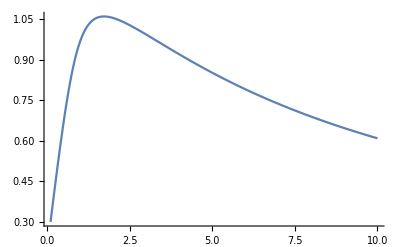

```mathematica
Plot[(term1/.{Subscript[w, p]->1,α->0.1,γ->10}),{Subscript[h, p],0.1,10}]
```

```mathematica
Manipulate[Plot[(term1/.{Subscript[w, p]->1,α->αm,γ->γm}),{Subscript[h, p],0.1,10}],{γm,0.1,10},{αm,0.1,10}]
```

```mathematica
Manipulate[plots/.{Subscript[w, p]->γm,Subscript[h, p]->αm},{γm,0.1,10},{αm,0.1,10}]
```